# Hints for a luminosity transition in the Cepheid SnIa calibrator data Leandros Perivolaropoulos and Foteini Skara The one dimensional relative probability density value of MB for all cases studied. All measurements are shown as normalized Gaussian distribution

```mathematica
op=0.003;
thi=0.004;
```

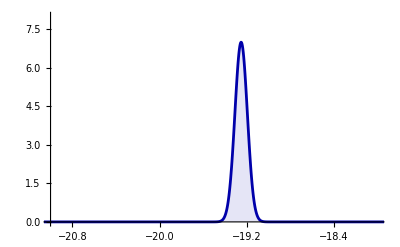

```mathematica
mbss=Plot[PDF[NormalDistribution[-19.251,0.057],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[0.005],Darker[Blue]},FillingStyle->Directive[Opacity[0.1]],Filling->Axis]
```

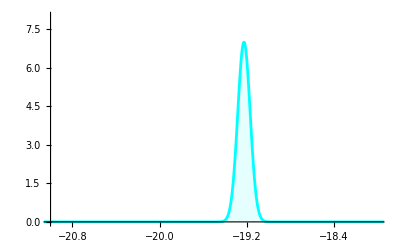

```mathematica
mbs=Plot[PDF[NormalDistribution[-19.225,0.057],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[0.005],Cyan},FillingStyle->Directive[Opacity[0.1]],Filling->Axis]
```

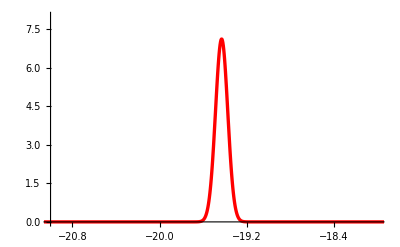

```mathematica
mbi=Plot[PDF[NormalDistribution[-19.43,0.056],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[thi+0.002],Red},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

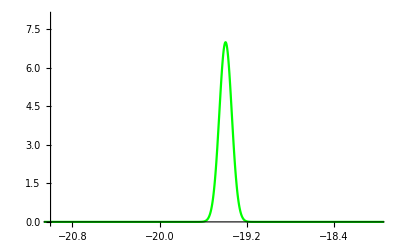

```mathematica
mbii=Plot[PDF[NormalDistribution[-19.394,0.057],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[thi],Green},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

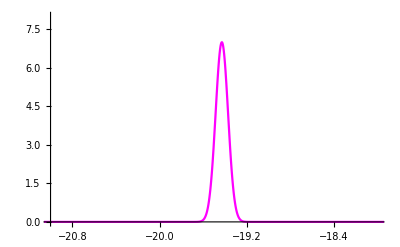

```mathematica
mbiii=Plot[PDF[NormalDistribution[-19.428,0.057],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[thi],Magenta},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

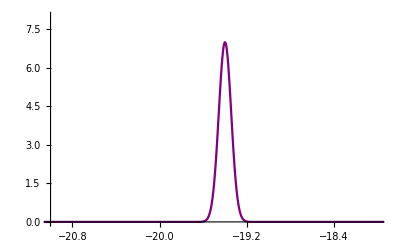

```mathematica
mbiv=Plot[PDF[NormalDistribution[-19.399,0.057],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[thi],Purple},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

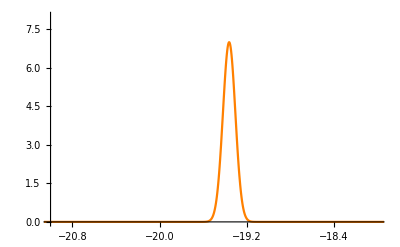

```mathematica
mbv=Plot[PDF[NormalDistribution[-19.361,0.057],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[thi],Orange},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

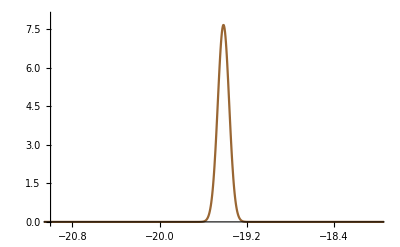

```mathematica
mbvi=Plot[PDF[NormalDistribution[-19.413,0.052],x],{x,-25,-12},PlotRange->{{-21,-18},{0,8}},PlotStyle->{PointSize->Large,Thickness[thi],Brown},FillingStyle->Directive[Opacity[op]],Filling->Axis]
```

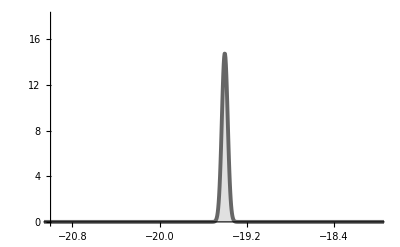

```mathematica
plhor=Plot[PDF[NormalDistribution[-19.401,0.027],x],{x,-25,-12},PlotRange->{{-21,-18},{0,18}},PlotStyle->{PointSize->Large,Thickness[0.007],RGBColor[0.4,0.4,0.4]},Filling->Axis]
```

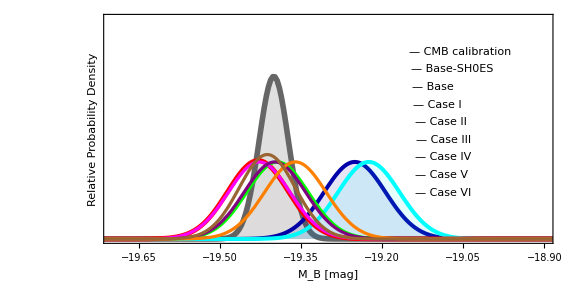

```mathematica
figprmb=Show[plhor,mbss,mbs,mbi,mbii,mbiii,mbiv,mbv,mbvi,Graphics[{Inset["— CMB calibration",{-19.056,17},BaseStyle->{Bold,RGBColor[0.4,0.4,0.4],FontFamily->"Times",14}]}],Graphics[{Inset["— Base-SH0ES",{-19.0715,15.4},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],
Graphics[{Inset["— Base ",{-19.106,13.8},BaseStyle->{Bold,Cyan,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case I",{-19.098,12.2},BaseStyle->{Bold,Red,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case II ",{-19.092,10.6},BaseStyle->{Bold,Green,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case III ",{-19.087,9},BaseStyle->{Bold,Magenta,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case IV ",{-19.087,7.4},BaseStyle->{Bold,Purple,FontFamily->"Times",14}]}],
Graphics[{Inset["— Case V ",{-19.09,5.8},BaseStyle->{Bold,Orange,FontFamily->"Times",14}]}],Graphics[{Inset["— Case VI ",{-19.087,4.2},BaseStyle->{Bold,Brown,FontFamily->"Times",14}]}],
PlotRange->{{-19.7,-18.9},{0,20}},LabelStyle->Directive[Bold,Italic,18,Black],FrameLabel->{"M_B   [mag]  ","Relative Probability Density"},Frame->True,BaseStyle->{FontFamily->"Times",8},FrameStyle->Directive[Black,Thickness[0.007]],FrameTicks->{{None,None},{All,None}},AspectRatio->0.5,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figprmb.pdf",figprmb,ImageResolution->1000];
```